# Logistic迭代 和倍增周期分叉图

## 迭代

### 定义函数f，迭代iter

```mathematica
f[a_:2]:=Function[x,a x(1-x)]
```

```mathematica
(*x0：起始点,m：最大迭代次数*)
iter[a_,m_:100,x0_:0.2]:=NestWhileList[f[a],x0,Count[{##},Last@{##}]==1&,All,m]
iter[2]
```

{0.2,0.32,0.4352,0.491602,0.499859,0.5,0.5,0.5,0.5}

使用UnsameQ性能差

```mathematica
(*x0：起始点,m：最大迭代次数*)
iter2[a_,m_:100,x0_:0.2]:=NestWhileList[f[a],x0,UnsameQ,All,m]
iter2[2]
```

{0.2,0.32,0.4352,0.491602,0.499859,0.5,0.5,0.5,0.5}

对比性能

```mathematica
Grid@Table[First@Timing@h[3,m],{h,{iter,iter2}},{m,{100,300,500,600}}]
```

0. | 0.015625 | 0.046875 | 0.046875
0.03125 | 0.75 | 3.57813 | 6.1875

```mathematica
Grid@Table[First@Timing@h[3,m],{h,{NestList[f[#1],0.2,#2]&,iter}},{m,{100,300,500,600,1000,2000,3000}}]
```

0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0.015625 | 0.03125 | 0.046875 | 0.140625 | 0.53125 | 1.20313

#### 说明使用NestList的性能远高于NestWhileList

### 可视化迭代

#### 选取不同的a值，从初值0 .1 开始迭代

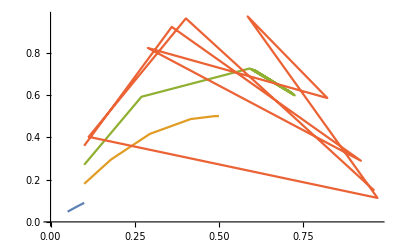

```mathematica
ListLinePlot[Table[Partition[iter[a,10,0.1],2,1],{a,1,4}]]
```

加入y=x上的点作为参考

```mathematica
lps[l_]:=ReplacePart[{1,2}->0]@Partition[Riffle[l,l],2,1]
lps[iter[2]]
```

{{0.2,0},{0.2,0.32},{0.32,0.32},{0.32,0.4352},{0.4352,0.4352},{0.4352,0.491602},{0.491602,0.491602},{0.491602,0.499859},{0.499859,0.499859},{0.499859,0.5},{0.5,0.5},{0.5,0.5},{0.5,0.5},{0.5,0.5},{0.5,0.5},{0.5,0.5},{0.5,0.5}}

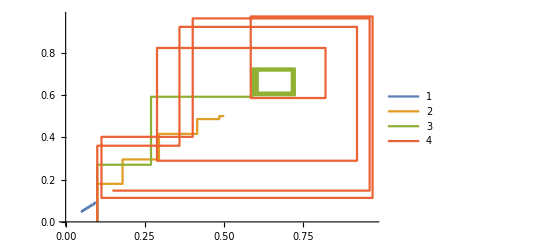

```mathematica
ListLinePlot[Table[lps[iter[a,10,0.1]],{a,1,4}],PlotLegends->Automatic]
```

```mathematica
Manipulate[
Show[Plot[{f[a][x],x},{x,-0.1,1.1},PlotRange->{{-0.1,1.1},{-0.1,1.1}},AspectRatio->1],
ListLinePlot[lps@iter[a,m,x0]
,PlotStyle->Pink,PlotRange->All]
],{{a,2},1,4},{m,10,100,1},{{x0,0.2},0,1},SaveDefinitions->True]
```

## 倍增周期分插图

临时效果

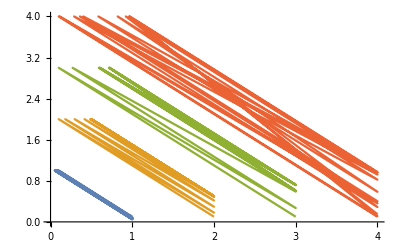

```mathematica
ListLinePlot[Table[Partition[Riffle[iter[a,10,0.1],a,{1,-2,2}],2,1],{a,1,4,1}]]
```

将上面的划分方式改为不重叠的，两个元素一组

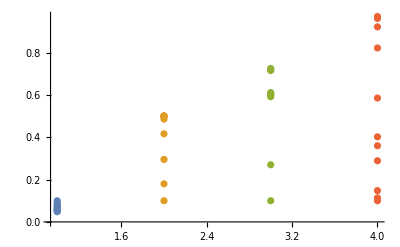

```mathematica
ListPlot[Table[Partition[Riffle[iter[a,10,0.1],a,{1,-2,2}],2],{a,1,4,1}]]
```

改变迭代次数，和a的取值间隔

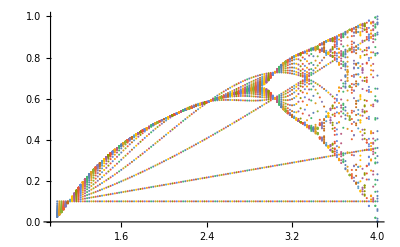

```mathematica
ListPlot[Table[Partition[Riffle[iter[a ,30,0.1],a,{1,-2,2}],2],{a,1,4,0.02}]]
```

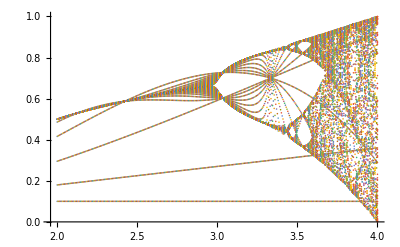

```mathematica
ListPlot[Table[Partition[Riffle[iter[a ,80,0.1],a,{1,-2,2}],2],{a,2,4,0.005}]]
```

#### 初始值x0只会影响迭代过程，不影响无限次迭代后的（周期性）收敛或发散

### 计算500次迭代后结果，如果发现周期性，只保留周期点

```mathematica
cal[a_,n_:500]:=Block[{l,p},l=iter[a,n];p=Position[l,l[[-1]]];p=If[Length[p]>1,p[[-2,1]],-10];l[[p;;-2]]]
```

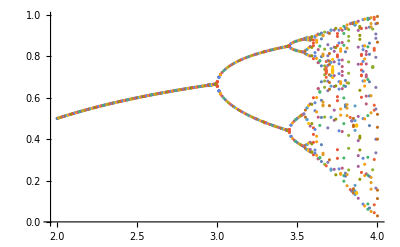

```mathematica
ListPlot[Table[Partition[Riffle[cal[a],a,{1,-2,2}],2],{a,2,4,0.01}]]
```

```mathematica
Manipulate[ListPlot[Table[Partition[Riffle[NestList[a #(1-#)&,0.1,m][[-d;;]],a,{1,-2,2}],2],{a,2,4,2/s}]],{{m,10,"迭代次数"},10,50,1},{{d,8,"保留"},1,m+1,1},{{s,50,"采样点"},10,300,1}]
```

## 另一种巧妙的绘图思路

Author: Benny Chang

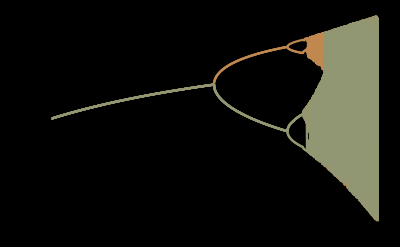

```mathematica
Plot[FixedPoint[x#(1-#)&,Range[10]/15.,1000],{x,2,4},ColorFunction->Function[{x,y},ColorData["Rainbow"][y]],Background->Black]
```

## 注意：15.不可以写成15，原因另见。

### 看看简单利用FixedPoint的效果

```mathematica
Manipulate[Plot[FixedPoint[a #(1-#)&,0.1,m],{a,2,4},PlotRange->{0,1}],{{m,10,"迭代次数"},10,50,1}]
```

### 他巧妙的利用不同初值迭代过程不一样的特点，将若干个绘图叠加在一起，妙啊

```mathematica
Manipulate[ListPlot[Table[{a,FixedPoint[a #(1-#)&,0.1,m]},{a,2,4,2/s}],PlotRange->1,PlotTheme->"Web"],{{m,10,"迭代次数"},10,50,1},{{s,50,"采样点"},10,300,1}]
```

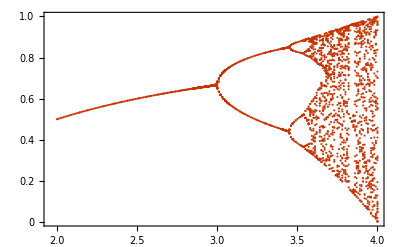

```mathematica
pr[l_,x_]:=Partition[Riffle[l,x,{1,-2,2}],2]
ListPlot[Union@@Table[pr[FixedPoint[a #(1-#)&,Range[50]/55.,200],a],{a,2,4,2/200}],PlotRange->1,PlotTheme->"Web"]
```